# NIUS project calculations

## Done by: Soumyadeep Sarma, Project under: Prof. Deepak Dhar

```mathematica
L=3;
f[z_]= Sum[Binomial[L-n+1,n] z^n,{n,0,(L+1)/2}]
s =Roots[f[z]==0,z]//FullSimplify;
t =NRoots[f[z]==0,z]//FullSimplify;
```

1+3 z+z^2

```mathematica
Solve[f[z]==0,z]//FullSimplify;
```

```mathematica
Solve[N[s[[2]],10]](*Checking for the roots*)
```

{{z→-0.26794919}}

```mathematica
g[z_]= Sum[Binomial[L-n+1,n] z^n,{n,1,(L+1)/2}];
k = Roots[g[z]==0,z]//FullSimplify;
Solve[N[k[[2]],10]]
```

{{z→-0.480508462-0.400470217 ⅈ}}

Diagonalizing T matrix for dimer on ladder problem

```mathematica
Clear[z]
```

```mathematica
l=25;
```

```mathematica
T=({{1+y, 1, 1}, {2y, y, 0}, {y^2, 0, 0}});
t=Eigenvalues[T];
w =Eigenvectors[T];
Subscript[v, i] = {1+y,2y,y^2};
v = MatrixPower[T,l-1].Subscript[v, i];
f[y_]=y;
g[y_]=v[[1]]//Expand
j = Roots[g[y]==0,y]//FullSimplify;
```

1+73 y+2486 y^2+52484 y^3+769991 y^4+8340715 y^5+69191458 y^6+450025410 y^7+2330671763 y^8+9708734933 y^9+32730048126 y^10+89567993976 y^11+199052281544 y^12+358551303670 y^13+521287815678 y^14+607714810652 y^15+562938292231 y^16+409378631641 y^17+230098439272 y^18+97969184844 y^19+30782211558 y^20+6893852746 y^21+1048772300 y^22+100861716 y^23+5416441 y^24+121393 y^25

```mathematica
data = Table[f[y]/.Solve[N[j[[i]],10]],{i,1,l}]
```

{{-13.62161864},{-9.043410265},{-5.69441346},{-3.708136343},{-2.546460502},{-1.838374442},{-1.384229725},{-1.078760513},{-0.8645596278},{-0.708848034},{-0.5920354307},{-0.5019219293},{-0.4306448654},{-0.3730126729},{-0.3255651182},{-0.2860155372},{-0.2528812316},{-0.225199725},{-0.2023018977},{-0.1836554762},{-0.1687875812},{-0.1572677008},{-0.1487194494},{-0.1428372672},{-0.1393980338}}

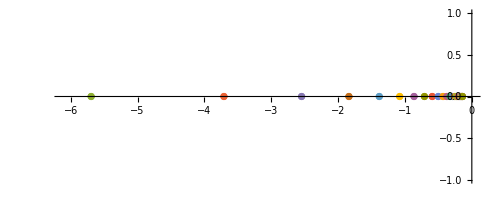

```mathematica
ComplexListPlot[data]
```